```mathematica
lib = "C://Projekte//Cheyette//Cheyette//x64//Debug//Cheyette";
SwapRate=LibraryFunctionLoad[ lib ,"SwapRate",{Real,Real,Real,{Real,2}},Real];
annuity=LibraryFunctionLoad[ lib ,"Annuity",{Real,Real,Real,{Real,2}},Real];
G2ESwaption=LibraryFunctionLoad[ lib ,"G2ESwaption",{Real,Real,Real,Real,Integer,Real,Real,Real,Real,Real,{Real,2}},Real];
G2ESwaption1=LibraryFunctionLoad[ lib ,"G2ESwaption1",{Real,Real,Real,Real,Integer,Real,Real,Real,Real,Real,{Real,2}},Real];
G2ESwaption2=LibraryFunctionLoad[ lib ,"G2ESwaption2",{Real,Real,Real,Real,Integer,Real,Real,Real,Real,Real,{Real,2}},{Real,1}];
G2ESwaptionIntegrand=LibraryFunctionLoad[ lib ,"G2ESwaptionIntegrand",{Real,Real,Real,Real,Integer,Real,Real,Real,Real,Real,{Real,2},Real},{Real,1}];
G2ESwaptionVtTfunc=LibraryFunctionLoad[ lib ,"G2ESwaptionVtTfunc",{Real,Real,Real,Real,Integer,Real,Real,Real,Real,Real,{Real,2}},{Real,1}];
ImpvolBlackFormula =LibraryFunctionLoad[ lib ,"ImpvolBlackFormula",{Real,Real,Real},Real];
ImpvolBlackFormulaV =LibraryFunctionLoad[ lib ,"ImpvolBlackFormulaVector",{Real,Real,Real},{Real,1}];
BlackVector =LibraryFunctionLoad[ lib ,"BlackVector",{Real,Real,Real},{Real,1}];
BL =LibraryFunctionLoad[ lib ,"BlackFormula",{Real,Real,Real},Real];
Discount = LibraryFunctionLoad[ lib ,"Discount",{Real,{Real,2}},Real];
```

```mathematica
zCurve={{0.,0.03},{0.004,0.030029985},{0.02,0.0301496256},{0.0833,0.0306182897},{0.25,0.0318176081},{0.5,0.0335250929},{0.75,0.0351291265},{1.,0.0366359765},{2.,0.0418040802},{3.,0.0458290034},{4.,0.0489636168},{5.,0.0514048561},{7.,0.0547867817},{10.,0.05753745},{12.,0.0585063879},{15.,0.0592944676},{20.,0.0597978616},{25.,0.0599420864},{30.,0.0599834075}};
```

```mathematica
T1 = 1.0;
T2 = 2.0;
Δt = 0.5;
{σ1,κ1,σ2,κ2,ρ} ={0.01095124531241437,0.19691640516187803,0.005055316759580264,0.19702295377230233,-0.4070687566179207};
```

```mathematica
K = F =SwapRate[T1,T2,Δt,zCurve[[All,{1,2}]]]
```

0.0474971

```mathematica
pr =G2ESwaption[T1,T2,Δt,K,1,σ1,σ2,κ1,κ2,ρ,zCurve[[All,{1,2}]]]
```

0.00314524

```mathematica
ann =annuity[T1,T2,Δt,zCurve[[All,{1,2}]]]
```

0.931329

```mathematica
ImpvolBlackFormula[ pr/ann,F,F]
```

0.178464

```mathematica
TCurve
```

{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.}

```mathematica
ZCurve= {1.5,1.52,1.55,1.56,1.57,1.51,1.42,1.39,1.41,1.51,1.6,1.89,2.05}/100
```

{0.015,0.0152,0.0155,0.0156,0.0157,0.0151,0.0142,0.0139,0.0141,0.0151,0.016,0.0189,0.0205}

```mathematica
TCurve ={0,1/12,2/12,3/12,6/12,1,2,3,5,7,10,20,30}
```

{0,1/12,1/6,1/4,1/2,1,2,3,5,7,10,20,30}

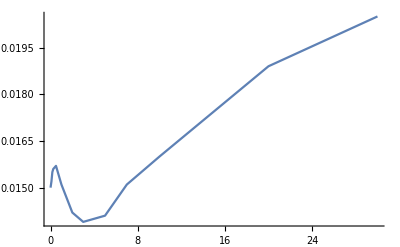

```mathematica
ListLinePlot[{TCurve,ZCurve}ᵀ]
```

```mathematica
zCurve={#,Interpolation[{TCurve,ZCurve}ᵀ,#]}& /@ Range[0,30,0.5]
```

{{0.,0.015},{0.5,0.0157},{1.,0.0151},{1.5,0.0142667},{2.,0.0142},{2.5,0.01396},{3.,0.0139},{3.5,0.0138575},{4.,0.01388},{4.5,0.0139625},{5.,0.0141},{5.5,0.0143125},{6.,0.01456},{6.5,0.0148275},{7.,0.0151},{7.5,0.0153625},{8.,0.0156},{8.5,0.0157975},{9.,0.01594},{9.5,0.0160125},{10.,0.016},{10.5,0.0161052},{11.,0.0162028},{11.5,0.0162948},{12.,0.0163831},{12.5,0.0164697},{13.,0.0165566},{13.5,0.0166458},{14.,0.0167391},{14.5,0.0168386},{15.,0.0169462},{15.5,0.0170638},{16.,0.0171935},{16.5,0.0173373},{17.,0.0174969},{17.5,0.0176745},{18.,0.017872},{18.5,0.0180913},{19.,0.0183345},{19.5,0.0186034},{20.,0.0189},{20.5,0.0190233},{21.,0.0191432},{21.5,0.0192594},{22.,0.0193718},{22.5,0.0194803},{23.,0.0195845},{23.5,0.0196844},{24.,0.0197797},{24.5,0.0198703},{25.,0.0199559},{25.5,0.0200365},{26.,0.0201117},{26.5,0.0201814},{27.,0.0202455},{27.5,0.0203036},{28.,0.0203558},{28.5,0.0204016},{29.,0.0204411},{29.5,0.020474},{30.,0.0205}}

```mathematica
SwaptionCube ={MarketSwaptionMats,MarketSwaptionTenors,MarketSwaptionVols}={{1.,5.,0.1996},{2.,5.,0.18280000000000002},{3.,5.,0.16820000000000002},{4.,5.,0.15560000000000002},{5.,5.,0.1448},{6.,5.,0.1355},{7.,5.,0.1275},{10.,5.,0.1092}}// Transpose;
```

```mathematica
{σ1,σ2, κ1, κ2,ρ} ={RandomReal[{0.0001,0.06}],RandomReal[{0.0001,0.06}],RandomReal[{0.0001,0.4}],RandomReal[{0.0001,0.4}],-RandomReal[]}
```

{0.0365965,0.051948,0.0509792,0.227008,-0.601297}

```mathematica
MarketSwaptionTenors
```

{5.,5.,5.,5.,5.,5.,5.,5.}

```mathematica
{σ1,σ2, κ1, κ2,ρ} ={RandomReal[{0.0001,0.06}],RandomReal[{0.0001,0.06}],RandomReal[{0.0001,0.4}],RandomReal[{0.0001,0.4}],-RandomReal[]};
{σ1,σ2, κ1, κ2,ρ,Table[
T1 = MarketSwaptionMats[[t1]];
T2 =T1+5;
pr =G2ESwaption[T1 ,T2,Δt,K,1,σ1,σ2,κ1,κ2,ρ,zCurve1];
K = F =SwapRate[T1,T2,Δt,zCurve1];
ann =annuity[T1,T2,Δt,zCurve1];
{T1,T2,ImpvolBlackFormula[ pr/ann,F,K],F,K},{t1 ,1,Length[MarketSwaptionMats]},{x ,1.5,Length[MarketSwaptionMats]}]}
```

{0.0162164,0.0509273,0.0498528,0.148692,-0.19147,{{{1.,6.,0.,0.0144774,0.0144774},{1.,6.,0.,0.0144774,0.0144774},{1.,6.,0.,0.0144774,0.0144774},{1.,6.,0.,0.0144774,0.0144774},{1.,6.,0.,0.0144774,0.0144774},{1.,6.,0.,0.0144774,0.0144774},{1.,6.,0.,0.0144774,0.0144774}},{{2.,7.,0.,0.0154779,0.0154779},{2.,7.,0.,0.0154779,0.0154779},{2.,7.,0.,0.0154779,0.0154779},{2.,7.,0.,0.0154779,0.0154779},{2.,7.,0.,0.0154779,0.0154779},{2.,7.,0.,0.0154779,0.0154779},{2.,7.,0.,0.0154779,0.0154779}},{{3.,8.,0.,0.0166415,0.0166415},{3.,8.,0.,0.0166415,0.0166415},{3.,8.,0.,0.0166415,0.0166415},{3.,8.,0.,0.0166415,0.0166415},{3.,8.,0.,0.0166415,0.0166415},{3.,8.,0.,0.0166415,0.0166415},{3.,8.,0.,0.0166415,0.0166415}},{{4.,9.,0.,0.0176306,0.0176306},{4.,9.,0.,0.0176306,0.0176306},{4.,9.,0.,0.0176306,0.0176306},{4.,9.,0.,0.0176306,0.0176306},{4.,9.,0.,0.0176306,0.0176306},{4.,9.,0.,0.0176306,0.0176306},{4.,9.,0.,0.0176306,0.0176306}},{{5.,10.,0.,0.0179814,0.0179814},{5.,10.,0.,0.0179814,0.0179814},{5.,10.,0.,0.0179814,0.0179814},{5.,10.,0.,0.0179814,0.0179814},{5.,10.,0.,0.0179814,0.0179814},{5.,10.,0.,0.0179814,0.0179814},{5.,10.,0.,0.0179814,0.0179814}},{{6.,11.,0.,0.0182677,0.0182677},{6.,11.,0.,0.0182677,0.0182677},{6.,11.,0.,0.0182677,0.0182677},{6.,11.,0.,0.0182677,0.0182677},{6.,11.,0.,0.0182677,0.0182677},{6.,11.,0.,0.0182677,0.0182677},{6.,11.,0.,0.0182677,0.0182677}},{{7.,12.,0.,0.0182702,0.0182702},{7.,12.,0.,0.0182702,0.0182702},{7.,12.,0.,0.0182702,0.0182702},{7.,12.,0.,0.0182702,0.0182702},{7.,12.,0.,0.0182702,0.0182702},{7.,12.,0.,0.0182702,0.0182702},{7.,12.,0.,0.0182702,0.0182702}},{{10.,15.,0.,0.0189119,0.0189119},{10.,15.,0.,0.0189119,0.0189119},{10.,15.,0.,0.0189119,0.0189119},{10.,15.,0.,0.0189119,0.0189119},{10.,15.,0.,0.0189119,0.0189119},{10.,15.,0.,0.0189119,0.0189119},{10.,15.,0.,0.0189119,0.0189119}}}}

```mathematica
impliedVol[T1_,T2_,m_,{σ1_,σ2_, κ1_, κ2_,ρ_}] := Module[{pr,F,K},
F =SwapRate[T1,T2,Δt,zCurve1];
K = m F;
pr =G2ESwaption[T1 ,T2,Δt,K,1,σ1,σ2,κ1,κ2,ρ,zCurve1];
ann =annuity[T1,T2,Δt,zCurve1];
ImpvolBlackFormula[ pr/ann,F,K]
]
```

```mathematica
impliedVol[T1,T2,1,{σ1,σ2, κ1, κ2,ρ}]
```

0.

```mathematica
Outer[impliedVol[{#1,#1+#2,#3}]&,{1,2,5},{1,2,5,10},{0.85,1,1.15},1,1]ᵀ // TableForm
```

impliedVol[{1,2,0.85}]
impliedVol[{1,2,1}]
impliedVol[{1,2,1.15}] | impliedVol[{2,3,0.85}]
impliedVol[{2,3,1}]
impliedVol[{2,3,1.15}] | impliedVol[{5,6,0.85}]
impliedVol[{5,6,1}]
impliedVol[{5,6,1.15}]
impliedVol[{1,3,0.85}]
impliedVol[{1,3,1}]
impliedVol[{1,3,1.15}] | impliedVol[{2,4,0.85}]
impliedVol[{2,4,1}]
impliedVol[{2,4,1.15}] | impliedVol[{5,7,0.85}]
impliedVol[{5,7,1}]
impliedVol[{5,7,1.15}]
impliedVol[{1,6,0.85}]
impliedVol[{1,6,1}]
impliedVol[{1,6,1.15}] | impliedVol[{2,7,0.85}]
impliedVol[{2,7,1}]
impliedVol[{2,7,1.15}] | impliedVol[{5,10,0.85}]
impliedVol[{5,10,1}]
impliedVol[{5,10,1.15}]
impliedVol[{1,11,0.85}]
impliedVol[{1,11,1}]
impliedVol[{1,11,1.15}] | impliedVol[{2,12,0.85}]
impliedVol[{2,12,1}]
impliedVol[{2,12,1.15}] | impliedVol[{5,15,0.85}]
impliedVol[{5,15,1}]
impliedVol[{5,15,1.15}]

```mathematica
p = {σ1,σ2, κ1, κ2,ρ}
```

{0.0162164,0.0509273,0.0498528,0.148692,-0.19147}

```mathematica
p={σ1,σ2, κ1, κ2,ρ} ={RandomReal[{0.0001,0.06}],RandomReal[{0.0001,0.06}],RandomReal[{0.0001,0.4}],RandomReal[{0.0001,0.4}],-RandomReal[]};
```

```mathematica
Flatten@{p,Outer[impliedVol[#1,#1+#2,#3,p]&,{1,2,5},{1,2,5,10},{0.85,1,1.15},1,1] }
```

{0.00138628,0.0197723,0.143778,0.0787732,-0.426667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.894599,0.823356,0.765936,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
zMax= Max[zCurve[[All,2]]]
```

0.0205

```mathematica
res =Table[
	p= {σ1,σ2, κ1, κ2,ρ}=Flatten@{RandomReal[{0.0001,zMax},2],RandomReal[{0.0001,2},2],-RandomReal[]};
	Flatten@{p,Outer[impliedVol[#1,#1+#2,#3,p]&,{1,2,5},{1,2,5,10},{0.85,1,1.15},1,1] },{100}];
```

```mathematica
res // TableForm
```

0.015668 | 0.0184324 | 1.81888 | 0.325099 | -0.738317 | 0.9557 | 0.877424 | 0.81441 | 0.864589 | 0.794722 | 0.738316 | 0.554184 | 0.511408 | 0.476636 | 0.30196 | 0.280154 | 0.262412 | 0. | 0. | 0. | 0. | 0. | 0.938289 | 0.656904 | 0.605842 | 0.564426 | 0.369027 | 0.342378 | 0.320714 | 0. | 0. | 0. | 0.992003 | 0.910672 | 0.845293 | 0.662516 | 0.611203 | 0.569596 | 0.394538 | 0.366225 | 0.343225
0.00635261 | 0.0159847 | 1.71745 | 1.19088 | -0.724229 | 0.390319 | 0.360142 | 0.335534 | 0.2588 | 0.239037 | 0.222905 | 0.107255 | 0.0993774 | 0.0929528 | 0.049434 | 0.0460835 | 0.0433611 | 0.41112 | 0.379295 | 0.353351 | 0.267097 | 0.2467 | 0.230051 | 0.105596 | 0.0978662 | 0.091564 | 0.0505086 | 0.0470988 | 0.044329 | 0.325545 | 0.300513 | 0.280087 | 0.207049 | 0.191336 | 0.178508 | 0.0920255 | 0.0853457 | 0.0799013 | 0.0467545 | 0.043637 | 0.0411056
0.00272724 | 0.016729 | 1.99373 | 1.6565 | -0.758799 | 0.327121 | 0.301932 | 0.281377 | 0.195864 | 0.180978 | 0.168823 | 0.0762006 | 0.0706414 | 0.066109 | 0. | 0.0326961 | 0. | 0.333431 | 0.307748 | 0.286792 | 0.195799 | 0.180924 | 0.168777 | 0.0727177 | 0.0674332 | 0.0631255 | 0. | 0.0323882 | 0. | 0.263036 | 0.242883 | 0.22643 | 0.151221 | 0.139802 | 0.130478 | 0.0631204 | 0.0585761 | 0.0548735 | 0. | 0.0298832 | 0.
0.015536 | 0.0150796 | 0.867693 | 1.96715 | -0.0124788 | 0.652331 | 0.600864 | 0.559083 | 0.445748 | 0.411352 | 0.383323 | 0.194985 | 0.180588 | 0.168823 | 0.0905207 | 0.0843427 | 0.0793234 | 0.70138 | 0.64577 | 0.600675 | 0.47102 | 0.434625 | 0.404965 | 0.196829 | 0.182354 | 0.170498 | 0.0948555 | 0.0884038 | 0.0831608 | 0.55712 | 0.513624 | 0.478248 | 0.367432 | 0.339327 | 0.316402 | 0.17303 | 0.160408 | 0.150067 | 0.0885967 | 0.0826443 | 0.0778082
0.0178918 | 0.0174243 | 1.41973 | 0.236615 | -0.18404 | 0. | 0. | 0. | 0. | 0.961929 | 0.892178 | 0.69273 | 0.638472 | 0.59449 | 0.403851 | 0.37419 | 0.350072 | 0. | 0. | 0. | 0. | 0. | 0. | 0.83538 | 0.768968 | 0.715335 | 0.502834 | 0.465725 | 0.435595 | 0. | 0. | 0. | 0. | 0. | 0. | 0.885486 | 0.814863 | 0.757922 | 0.565123 | 0.523457 | 0.48967
0.000980119 | 0.0200233 | 0.870237 | 0.308453 | -0.946976 | 0. | 0. | 0. | 0. | 0.991633 | 0.919429 | 0.669312 | 0.617185 | 0.574907 | 0.364673 | 0.338278 | 0.316815 | 0. | 0. | 0. | 0. | 0. | 0. | 0.784164 | 0.722426 | 0.672505 | 0.441344 | 0.409325 | 0.383319 | 0. | 0. | 0. | 0. | 0. | 0. | 0.789465 | 0.727505 | 0.67742 | 0.471947 | 0.437876 | 0.410226
0.0161164 | 0.0147263 | 0.0898021 | 1.11337 | -0.270546 | 0. | 0. | 0. | 0. | 0. | 0.998879 | 0.941974 | 0.872572 | 0.806147 | 0.677601 | 0.637208 | 0.585748 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.906724 | 0.853277 | 0.790194 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0163293 | 0.00750803 | 0.893152 | 1.59701 | -0.595582 | 0.528071 | 0.487041 | 0.453292 | 0.377522 | 0.348716 | 0.324774 | 0.168773 | 0.156605 | 0.146061 | 0.0783532 | 0.0732033 | 0.0686104 | 0.577613 | 0.532692 | 0.495522 | 0.404004 | 0.37335 | 0.34748 | 0.172034 | 0.159812 | 0.148944 | 0.0828559 | 0.0775284 | 0.0726794 | 0.461697 | 0.426162 | 0.396724 | 0.316616 | 0.292476 | 0.272677 | 0.151924 | 0.140857 | 0.131687 | 0.0776073 | 0.0726167 | 0.0680723
0.00793094 | 0.0025252 | 1.47037 | 1.52258 | -0.624473 | 0.162678 | 0.150239 | 0.140046 | 0.100454 | 0.0928367 | 0.0865999 | 0. | 0.0368271 | 0. | 0. | 0.0170514 | 0. | 0.166985 | 0.154219 | 0.143752 | 0.101146 | 0.0934807 | 0.0872014 | 0. | 0.035408 | 0. | 0. | 0.0170129 | 0. | 0.132008 | 0.121932 | 0.113695 | 0.0781926 | 0.0723045 | 0.0674676 | 0. | 0.0307753 | 0. | 0. | 0.0157067 | 0.
0.0123929 | 0.019711 | 1.82977 | 1.5321 | -0.285523 | 0.4582 | 0.422645 | 0.393681 | 0.276556 | 0.255473 | 0.238267 | 0.108131 | 0.100233 | 0.0937947 | 0.0497373 | 0.0463895 | 0.0436703 | 0.46847 | 0.432093 | 0.402463 | 0.277314 | 0.256179 | 0.238931 | 0.103508 | 0.0959771 | 0.0898386 | 0.0494079 | 0.0460962 | 0.0434069 | 0.369043 | 0.340625 | 0.317449 | 0.214096 | 0.197896 | 0.184672 | 0.0898656 | 0.0833882 | 0.0781106 | 0.0455561 | 0.0425425 | 0.040096
0.014406 | 0.0190315 | 1.33069 | 0.118345 | -0.27929 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.960243 | 0.890962 | 0.715086 | 0.659801 | 0.615042 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.946735 | 0.871527 | 0.811036 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00470227 | 0.00270448 | 1.06521 | 0.911907 | -0.291696 | 0.155363 | 0.143463 | 0.13374 | 0.105691 | 0.0976491 | 0.0910785 | 0.0451122 | 0.0417955 | 0.0390887 | 0. | 0.019444 | 0. | 0.165085 | 0.152438 | 0.142104 | 0.110202 | 0.101818 | 0.0949685 | 0.0449117 | 0.0416204 | 0.0389347 | 0. | 0.0200964 | 0. | 0.131431 | 0.121389 | 0.113184 | 0.0858009 | 0.0793021 | 0.073993 | 0. | 0.0364252 | 0. | 0. | 0.0186858 | 0.
0.00942989 | 0.00120359 | 1.62287 | 1.77189 | -0.856067 | 0.185286 | 0.175093 | 0.159467 | 0.111572 | 0.105466 | 0.0961422 | 0.0433786 | 0.0412754 | 0.0377132 | 0. | 0.0191067 | 0. | 0.188814 | 0.178581 | 0.16252 | 0.111611 | 0.105516 | 0.0961803 | 0. | 0.0394321 | 0. | 0. | 0.0189416 | 0. | 0.152554 | 0.141089 | 0.13136 | 0.0869471 | 0.0815679 | 0.0751437 | 0. | 0.0342557 | 0. | 0. | 0.0174777 | 0.
0.0119811 | 0.000940803 | 1.20597 | 1.84178 | -0.0821686 | 0.352947 | 0.327174 | 0.303365 | 0.227631 | 0.212877 | 0.196337 | 0.0942725 | 0.0874507 | 0.0817797 | 0.0426276 | 0.040538 | 0.0370283 | 0.367936 | 0.341717 | 0.316178 | 0.233755 | 0.218038 | 0.201603 | 0.091882 | 0.0855071 | 0.0798365 | 0.0429376 | 0.0411355 | 0.0376085 | 0.29297 | 0.270479 | 0.25212 | 0.178828 | 0.16894 | 0.153998 | 0.0788142 | 0.074486 | 0.0681703 | 0. | 0.0380682 | 0.
0.00489982 | 0.0133154 | 0.688962 | 1.72955 | -0.815465 | 0.169014 | 0.156077 | 0.145507 | 0.105063 | 0.0970761 | 0.0905506 | 0.0477095 | 0.0441736 | 0.0412877 | 0. | 0.0210039 | 0. | 0.184984 | 0.170814 | 0.159238 | 0.118987 | 0.109931 | 0.102532 | 0.0531931 | 0.0492546 | 0.0460408 | 0. | 0.0243579 | 0. | 0.152447 | 0.140803 | 0.131289 | 0.0973498 | 0.0899699 | 0.083941 | 0.0491052 | 0.0454922 | 0.0425447 | 0. | 0.0239051 | 0.
0.0196815 | 0.0201806 | 1.11344 | 1.97506 | -0.638936 | 0.484403 | 0.446722 | 0.416036 | 0.324556 | 0.299691 | 0.279406 | 0.136435 | 0.126394 | 0.118206 | 0.062939 | 0.058664 | 0.0551908 | 0.516293 | 0.476036 | 0.44327 | 0.339298 | 0.313292 | 0.292079 | 0.136073 | 0.126092 | 0.117954 | 0.0651459 | 0.0607383 | 0.057158 | 0.409384 | 0.37776 | 0.351981 | 0.263576 | 0.243523 | 0.227157 | 0.118905 | 0.110255 | 0.103204 | 0.0604722 | 0.0564299 | 0.0531481
0.00365296 | 0.0201054 | 0.40911 | 0.444254 | -0.272589 | 0. | 0. | 0.930444 | 0.884822 | 0.813269 | 0.755542 | 0.486503 | 0.44944 | 0.419291 | 0.244131 | 0.22689 | 0.21287 | 0. | 0. | 0. | 0. | 0.957407 | 0.888146 | 0.541953 | 0.500573 | 0.466947 | 0.281834 | 0.261956 | 0.2458 | 0. | 0. | 0.953334 | 0.866044 | 0.796387 | 0.740165 | 0.510853 | 0.472128 | 0.440651 | 0.282539 | 0.262784 | 0.246733
0.0015863 | 0.00401024 | 1.69821 | 1.5905 | -0.561434 | 0.0765785 | 0.0707254 | 0.0659414 | 0.0463368 | 0.042825 | 0.0399547 | 0. | 0.0168043 | 0. | 0. | 0.00777943 | 0. | 0.0781882 | 0.072212 | 0.0673273 | 0.0464102 | 0.0428939 | 0.0400201 | 0. | 0.0160721 | 0. | 0. | 0.007721 | 0. | 0.0617927 | 0.0570809 | 0.05323 | 0. | 0.0331664 | 0. | 0. | 0.0139636 | 0. | 0. | 0.00712492 | 0.
0.0127405 | 0.00296367 | 0.945537 | 0.0589773 | -0.283306 | 0.450147 | 0.415201 | 0.386728 | 0.332605 | 0.307055 | 0.286209 | 0.20006 | 0.184909 | 0.17254 | 0.142348 | 0.13168 | 0.122974 | 0.51108 | 0.471226 | 0.438784 | 0.387635 | 0.357746 | 0.333376 | 0.24607 | 0.227348 | 0.212066 | 0.189137 | 0.174896 | 0.163274 | 0.47822 | 0.441074 | 0.410823 | 0.383145 | 0.353645 | 0.329591 | 0.304865 | 0.28158 | 0.262582 | 0.255348 | 0.236081 | 0.220364
0.0136564 | 0.0141487 | 0.0512298 | 0.398174 | -0.168283 | 0. | 0. | 0. | 0. | 0. | 0. | 0.937039 | 0.860876 | 0.799537 | 0.707692 | 0.652455 | 0.607546 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.959816 | 0.882801 | 0.820394 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0167536 | 0.0170208 | 1.97308 | 0.374674 | -0.805989 | 0.798554 | 0.734464 | 0.68262 | 0.719884 | 0.662691 | 0.616334 | 0.44691 | 0.412745 | 0.384928 | 0.236041 | 0.219148 | 0.205401 | 0. | 0.965758 | 0.895553 | 0.905404 | 0.831892 | 0.772619 | 0.522737 | 0.482657 | 0.450067 | 0.285 | 0.264642 | 0.248084 | 0.958756 | 0.88034 | 0.817225 | 0.795947 | 0.732374 | 0.680955 | 0.514737 | 0.475473 | 0.443549 | 0.297645 | 0.27655 | 0.259402
0.00270757 | 0.0111155 | 1.86383 | 0.557083 | -0.167705 | 0.541633 | 0.499285 | 0.46483 | 0.425467 | 0.392583 | 0.365783 | 0.220322 | 0.203842 | 0.190399 | 0.106892 | 0.0994506 | 0.0933983 | 0.627893 | 0.578434 | 0.53826 | 0.482724 | 0.445277 | 0.414786 | 0.237978 | 0.220208 | 0.205716 | 0.119805 | 0.111489 | 0.104727 | 0.521624 | 0.480978 | 0.4479 | 0.392529 | 0.362349 | 0.337747 | 0.217779 | 0.201619 | 0.188442 | 0.116493 | 0.108486 | 0.101978
0.00461765 | 0.00915491 | 1.95045 | 1.97468 | -0.88021 | 0.0978469 | 0.0903699 | 0.0842591 | 0.0558513 | 0.0516242 | 0.0481707 | 0. | 0.0197913 | 0. | 0. | 0.00916151 | 0. | 0.0987623 | 0.0912153 | 0.0850472 | 0.0553013 | 0.0511174 | 0.0476992 | 0. | 0.0187149 | 0. | 0. | 0.00898936 | 0. | 0.0779964 | 0.0720518 | 0.0671937 | 0.0427183 | 0.039507 | 0.0368816 | 0. | 0.0162525 | 0. | 0. | 0.00829087 | 0.
0.0119637 | 0.00965593 | 1.94715 | 1.00308 | -0.793142 | 0.211179 | 0.194976 | 0.181739 | 0.150673 | 0.139183 | 0.129796 | 0.0667129 | 0.0617874 | 0.0577688 | 0. | 0.0287927 | 0. | 0.23305 | 0.215156 | 0.20054 | 0.16281 | 0.150395 | 0.140253 | 0.0686175 | 0.0635677 | 0.0594486 | 0. | 0.030741 | 0. | 0.187128 | 0.172808 | 0.161109 | 0.127707 | 0.118011 | 0.110091 | 0.060417 | 0.0560036 | 0.0524049 | 0. | 0.0287755 | 0.
0.00577437 | 0.0155819 | 1.93877 | 1.43815 | -0.341555 | 0.367066 | 0.338736 | 0.315628 | 0.227513 | 0.210188 | 0.196044 | 0.090176 | 0.0835823 | 0.0782061 | 0. | 0.0386954 | 0. | 0.377683 | 0.348517 | 0.32473 | 0.229579 | 0.212101 | 0.197833 | 0.0868578 | 0.0805305 | 0.0753723 | 0. | 0.0386901 | 0. | 0.298074 | 0.275196 | 0.256523 | 0.177412 | 0.16399 | 0.153031 | 0.0754521 | 0.0700051 | 0.0655665 | 0. | 0.0357272 | 0.
0.013038 | 0.0170633 | 0.719466 | 0.0533727 | -0.983785 | 0.822806 | 0.756535 | 0.702962 | 0.928146 | 0.852285 | 0.791149 | 0.944095 | 0.866733 | 0.804355 | 0.79452 | 0.73113 | 0.679705 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.949628 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0069087 | 0.0148562 | 0.366343 | 0.929827 | -0.295803 | 0.571872 | 0.527062 | 0.490624 | 0.426332 | 0.393408 | 0.366577 | 0.220176 | 0.203689 | 0.19024 | 0.111437 | 0.103605 | 0.097232 | 0.647294 | 0.596225 | 0.554761 | 0.480322 | 0.443089 | 0.41277 | 0.242486 | 0.224327 | 0.209517 | 0.128496 | 0.119462 | 0.112113 | 0.543836 | 0.501395 | 0.466869 | 0.400839 | 0.370016 | 0.344892 | 0.232232 | 0.214914 | 0.200792 | 0.131525 | 0.122339 | 0.114869
0.0203949 | 0.0130745 | 0.71983 | 1.55037 | -0.451396 | 0.8014 | 0.737127 | 0.685126 | 0.595637 | 0.549161 | 0.511189 | 0.283175 | 0.262044 | 0.244822 | 0.133258 | 0.124095 | 0.116619 | 0.9057 | 0.832121 | 0.77274 | 0.657539 | 0.606098 | 0.563863 | 0.297391 | 0.275244 | 0.257182 | 0.14525 | 0.135262 | 0.127128 | 0.730265 | 0.672309 | 0.625276 | 0.520591 | 0.480532 | 0.447453 | 0.265778 | 0.246179 | 0.230167 | 0.137977 | 0.12861 | 0.120993
0.00598291 | 0.0131055 | 0.419874 | 0.233438 | -0.913384 | 0.578201 | 0.53283 | 0.49594 | 0.535067 | 0.493269 | 0.459258 | 0.388137 | 0.358378 | 0.334121 | 0.239501 | 0.221905 | 0.207567 | 0.768529 | 0.707071 | 0.657316 | 0.693913 | 0.638929 | 0.594336 | 0.475028 | 0.438454 | 0.408679 | 0.302566 | 0.280329 | 0.262222 | 0.778836 | 0.716584 | 0.666205 | 0.682866 | 0.628941 | 0.5852 | 0.520781 | 0.480676 | 0.448057 | 0.349743 | 0.324141 | 0.303308
0.00712086 | 0.0151895 | 0.168064 | 0.000542115 | -0.445597 | 0. | 0. | 0.997167 | 0. | 0. | 0.999406 | 0. | 0.995851 | 0.923122 | 0.969426 | 0.889791 | 0.825711 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.000733046 | 0.01939 | 0.185445 | 1.49058 | -0.826568 | 0.43069 | 0.397333 | 0.370147 | 0.252679 | 0.233448 | 0.217751 | 0.0896237 | 0.08313 | 0.0778376 | 0. | 0.035601 | 0. | 0.437745 | 0.403826 | 0.376185 | 0.251329 | 0.232208 | 0.216601 | 0.0855715 | 0.0793901 | 0.0743532 | 0. | 0.0359936 | 0. | 0.346122 | 0.319504 | 0.297789 | 0.19613 | 0.181307 | 0.169206 | 0.0781625 | 0.0725418 | 0.0679628 | 0. | 0.0368877 | 0.
0.0100385 | 0.013796 | 0.642034 | 0.688253 | -0.193336 | 0.693147 | 0.638208 | 0.593649 | 0.519917 | 0.4795 | 0.446611 | 0.250909 | 0.232199 | 0.216944 | 0.118803 | 0.1106 | 0.103931 | 0.782465 | 0.71984 | 0.669161 | 0.574071 | 0.529258 | 0.492827 | 0.263801 | 0.24417 | 0.228169 | 0.129626 | 0.120703 | 0.113452 | 0.634135 | 0.584256 | 0.543752 | 0.456369 | 0.421178 | 0.392518 | 0.236483 | 0.219013 | 0.204774 | 0.1235 | 0.115089 | 0.108256
0.00360716 | 0.0191884 | 0.444986 | 0.709495 | -0.981343 | 0.643528 | 0.592977 | 0.551577 | 0.463126 | 0.427397 | 0.398123 | 0.206772 | 0.191478 | 0.178972 | 0.0945609 | 0.0881119 | 0.082871 | 0.707797 | 0.651667 | 0.606077 | 0.497499 | 0.458955 | 0.427541 | 0.210765 | 0.195207 | 0.182518 | 0.0998094 | 0.0930335 | 0.0875277 | 0.564746 | 0.520609 | 0.484716 | 0.388865 | 0.359043 | 0.334734 | 0.185197 | 0.171634 | 0.16058 | 0.0930993 | 0.0868551 | 0.0817852
0.00211542 | 0.00552985 | 0.15329 | 1.9893 | -0.895246 | 0.0917766 | 0.084742 | 0.0789915 | 0.0994816 | 0.0918431 | 0.0855968 | 0.0874009 | 0.0810894 | 0.0752781 | 0.0605102 | 0.0564789 | 0.0521971 | 0.148958 | 0.137531 | 0.128193 | 0.14747 | 0.136156 | 0.126905 | 0.114427 | 0.106857 | 0.0985841 | 0.0801767 | 0.0755909 | 0.069308 | 0.1751 | 0.161685 | 0.150723 | 0.162283 | 0.149955 | 0.139704 | 0.136787 | 0.126639 | 0.117981 | 0.100972 | 0.093707 | 0.0872768
0.0014328 | 0.0102021 | 1.39454 | 0.646918 | -0.126422 | 0.460788 | 0.424981 | 0.395809 | 0.350623 | 0.323657 | 0.301661 | 0.17238 | 0.159547 | 0.149077 | 0.0820379 | 0.0763671 | 0.0717562 | 0.521743 | 0.48102 | 0.447875 | 0.388914 | 0.358947 | 0.334513 | 0.182234 | 0.168698 | 0.157657 | 0.0900066 | 0.0838052 | 0.0787638 | 0.42657 | 0.393558 | 0.366652 | 0.311208 | 0.287402 | 0.267978 | 0.164009 | 0.151906 | 0.142036 | 0.0860651 | 0.0801968 | 0.0754284
0.00474686 | 0.0182402 | 1.25102 | 0.761409 | -0.420885 | 0.71759 | 0.660574 | 0.614357 | 0.525506 | 0.484656 | 0.451418 | 0.244456 | 0.226274 | 0.211451 | 0.114531 | 0.106658 | 0.100258 | 0.799046 | 0.734976 | 0.683152 | 0.572147 | 0.527513 | 0.491227 | 0.253396 | 0.234596 | 0.219271 | 0.1232 | 0.11476 | 0.107901 | 0.64139 | 0.590912 | 0.549928 | 0.450682 | 0.415965 | 0.387689 | 0.225081 | 0.208509 | 0.195003 | 0.116299 | 0.108419 | 0.102019
0.0200686 | 0.00343401 | 1.83021 | 1.73591 | -0.0662746 | 0.39265 | 0.363103 | 0.337544 | 0.227852 | 0.210953 | 0.196426 | 0.0875379 | 0.0813128 | 0.0759984 | 0. | 0.0376317 | 0. | 0.397712 | 0.367809 | 0.341881 | 0.22636 | 0.209594 | 0.195153 | 0.0828906 | 0.0771496 | 0.0719955 | 0. | 0.0370507 | 0. | 0.314029 | 0.289994 | 0.270237 | 0.174565 | 0.161885 | 0.150615 | 0.0721875 | 0.0669989 | 0.0627537 | 0. | 0.0341748 | 0.
0.0185035 | 0.00641617 | 0.66817 | 1.77595 | -0.733814 | 0.747854 | 0.695881 | 0.640191 | 0.572496 | 0.537537 | 0.491388 | 0.286781 | 0.265372 | 0.247896 | 0.13555 | 0.126657 | 0.118869 | 0.861045 | 0.800428 | 0.735813 | 0.640637 | 0.602083 | 0.549795 | 0.304836 | 0.282089 | 0.26338 | 0.149989 | 0.139669 | 0.131011 | 0.699602 | 0.653079 | 0.59958 | 0.511894 | 0.481036 | 0.439552 | 0.274023 | 0.253989 | 0.237391 | 0.143432 | 0.133681 | 0.125714
0.0188823 | 0.00401208 | 0.37907 | 0.439559 | -0.804431 | 0.94221 | 0.871092 | 0.803645 | 0.787694 | 0.731026 | 0.674291 | 0.463531 | 0.431793 | 0.398817 | 0.243327 | 0.226984 | 0.2124 | 0. | 0. | 0.99206 | 0.95127 | 0.880474 | 0.812136 | 0.527504 | 0.492294 | 0.453968 | 0.288734 | 0.268179 | 0.251439 | 0. | 0.945396 | 0.871701 | 0.815439 | 0.757384 | 0.698373 | 0.512641 | 0.47867 | 0.441375 | 0.298281 | 0.277141 | 0.259861
0.0179979 | 0.00644014 | 0.420793 | 0.625817 | -0.418175 | 0.93773 | 0.861224 | 0.799477 | 0.771166 | 0.709815 | 0.659872 | 0.437494 | 0.404481 | 0.377105 | 0.223164 | 0.20754 | 0.194559 | 0. | 0. | 0.971063 | 0.916741 | 0.842571 | 0.782318 | 0.492077 | 0.455097 | 0.424054 | 0.260469 | 0.242106 | 0.227116 | 0.984262 | 0.903719 | 0.838569 | 0.773134 | 0.712064 | 0.661896 | 0.469807 | 0.434854 | 0.405209 | 0.26443 | 0.245947 | 0.230867
0.0171657 | 0.00387119 | 0.444617 | 0.705831 | -0.370948 | 0.902688 | 0.832177 | 0.770354 | 0.734825 | 0.680422 | 0.629408 | 0.410191 | 0.381142 | 0.353228 | 0.205863 | 0.19337 | 0.17984 | 0. | 0. | 0.928307 | 0.866121 | 0.801343 | 0.740445 | 0.456744 | 0.425659 | 0.393235 | 0.239543 | 0.223912 | 0.209562 | 0.929936 | 0.858665 | 0.79361 | 0.722862 | 0.67135 | 0.61978 | 0.432334 | 0.402901 | 0.372328 | 0.240787 | 0.225303 | 0.211028
0.00623735 | 0.0176616 | 0.810325 | 1.30433 | -0.0157553 | 0.543114 | 0.500684 | 0.466166 | 0.353915 | 0.326781 | 0.304653 | 0.147166 | 0.136346 | 0.127523 | 0.0680122 | 0.0633973 | 0.0596482 | 0.570091 | 0.525455 | 0.489159 | 0.365016 | 0.337021 | 0.314193 | 0.145227 | 0.134583 | 0.125905 | 0.0696778 | 0.0649668 | 0.0611403 | 0.450871 | 0.415957 | 0.387513 | 0.283271 | 0.261721 | 0.244138 | 0.126935 | 0.11771 | 0.110191 | 0.064701 | 0.0603788 | 0.05687
0.0204696 | 0.0158221 | 1.55596 | 0.663632 | -0.749175 | 0.487514 | 0.449556 | 0.418645 | 0.381595 | 0.352171 | 0.328176 | 0.195081 | 0.180499 | 0.168603 | 0.0932253 | 0.0867506 | 0.0814848 | 0.574893 | 0.529822 | 0.493175 | 0.440945 | 0.40683 | 0.379033 | 0.213608 | 0.197678 | 0.184685 | 0.105834 | 0.0985114 | 0.0925572 | 0.479655 | 0.442397 | 0.412055 | 0.359161 | 0.331592 | 0.30911 | 0.195073 | 0.18062 | 0.168833 | 0.102648 | 0.0956194 | 0.0899075
0.000316499 | 0.0184432 | 0.353691 | 1.68229 | -0.211571 | 0.39019 | 0.360047 | 0.335467 | 0.230638 | 0.213097 | 0.198776 | 0.0889753 | 0.0824882 | 0.0771997 | 0. | 0.0381215 | 0. | 0.396811 | 0.366145 | 0.34114 | 0.230071 | 0.212578 | 0.198298 | 0.0847962 | 0.0786375 | 0.0736176 | 0. | 0.0377324 | 0. | 0.31286 | 0.288842 | 0.269242 | 0.177755 | 0.16433 | 0.153369 | 0.0737398 | 0.068434 | 0.0641112 | 0. | 0.0349024 | 0.
0.00488388 | 0.0195037 | 1.50845 | 0.363612 | -0.391296 | 0. | 0. | 0.974134 | 0.967882 | 0.888658 | 0.824914 | 0.572479 | 0.528394 | 0.492577 | 0.300283 | 0.278793 | 0.261316 | 0. | 0. | 0. | 0. | 0. | 0. | 0.657576 | 0.606635 | 0.565325 | 0.356828 | 0.331287 | 0.310531 | 0. | 0. | 0. | 0. | 0.935238 | 0.867938 | 0.642517 | 0.593024 | 0.552883 | 0.370568 | 0.344231 | 0.322839
0.000277148 | 0.019755 | 0.44562 | 0.657637 | -0.173511 | 0.910475 | 0.836427 | 0.776729 | 0.681983 | 0.628194 | 0.584564 | 0.329378 | 0.304723 | 0.284635 | 0.156021 | 0.145231 | 0.13646 | 0. | 0.949645 | 0.880829 | 0.756631 | 0.696491 | 0.647799 | 0.347306 | 0.321352 | 0.300213 | 0.170696 | 0.158926 | 0.149362 | 0.835186 | 0.768042 | 0.71379 | 0.600353 | 0.55353 | 0.515491 | 0.311732 | 0.288621 | 0.269795 | 0.162886 | 0.151774 | 0.142748
0.00413851 | 0.00166571 | 1.0306 | 0.0382226 | -0.0521978 | 0.185282 | 0.17107 | 0.159458 | 0.155253 | 0.143375 | 0.13367 | 0.117017 | 0.108104 | 0.100822 | 0.0918848 | 0.0849413 | 0.0792701 | 0.228337 | 0.210797 | 0.196469 | 0.196652 | 0.181581 | 0.169269 | 0.149003 | 0.137638 | 0.128353 | 0.123097 | 0.113782 | 0.106174 | 0.241297 | 0.222779 | 0.207656 | 0.213726 | 0.197361 | 0.183994 | 0.190286 | 0.175761 | 0.163898 | 0.168438 | 0.155689 | 0.145279
0.016972 | 0.0181565 | 0.0372081 | 0.298225 | -0.253491 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.940335 | 0.864447 | 0.803354 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.012908 | 0.00411362 | 0.556298 | 0.0515382 | -0.93547 | 0.355959 | 0.328486 | 0.306068 | 0.238634 | 0.220413 | 0.205537 | 0.101272 | 0.0935893 | 0.0873149 | 0.105511 | 0.0970237 | 0.0900677 | 0.382923 | 0.353321 | 0.32918 | 0.258903 | 0.239104 | 0.22294 | 0.153323 | 0.1415 | 0.131837 | 0.166926 | 0.153695 | 0.142863 | 0.379782 | 0.350464 | 0.326554 | 0.309205 | 0.285465 | 0.266092 | 0.285845 | 0.263769 | 0.245743 | 0.285885 | 0.263687 | 0.245555
0.0022684 | 0.015733 | 0.739692 | 1.12035 | -0.793403 | 0.420984 | 0.38838 | 0.361803 | 0.273846 | 0.252932 | 0.235861 | 0.111389 | 0.103219 | 0.0965577 | 0.0511794 | 0.0477184 | 0.0449067 | 0.440227 | 0.406091 | 0.378273 | 0.280581 | 0.259153 | 0.241664 | 0.108836 | 0.100882 | 0.0943977 | 0.0518904 | 0.0483957 | 0.0455573 | 0.34795 | 0.321169 | 0.299322 | 0.217171 | 0.200695 | 0.187245 | 0.0947196 | 0.0878574 | 0.0822649 | 0.0479669 | 0.0447769 | 0.0421871
0.0157858 | 0.0161716 | 0.461345 | 0.54843 | -0.24111 | 0. | 0.962448 | 0.892557 | 0.830156 | 0.763513 | 0.709661 | 0.440198 | 0.406839 | 0.379687 | 0.216969 | 0.201737 | 0.189353 | 0. | 0. | 0. | 0.962187 | 0.883596 | 0.820353 | 0.483292 | 0.446636 | 0.416823 | 0.247086 | 0.229772 | 0.215698 | 0. | 0.953449 | 0.884441 | 0.787292 | 0.724606 | 0.673899 | 0.449122 | 0.41531 | 0.387804 | 0.244298 | 0.227335 | 0.213552
0.0120995 | 0.00389499 | 1.87508 | 0.0297679 | -0.368515 | 0.319599 | 0.294961 | 0.274852 | 0.290441 | 0.26808 | 0.249825 | 0.256964 | 0.237206 | 0.221071 | 0.215867 | 0.199372 | 0.185901 | 0.434129 | 0.400435 | 0.372973 | 0.404251 | 0.372937 | 0.347405 | 0.341681 | 0.315336 | 0.293841 | 0.295841 | 0.273202 | 0.254726 | 0.519917 | 0.479378 | 0.446385 | 0.48284 | 0.445313 | 0.414752 | 0.455927 | 0.4206 | 0.391822 | 0.416032 | 0.384072 | 0.358031
0.016999 | 0.0113658 | 0.835302 | 0.885744 | -0.122319 | 0.753229 | 0.693159 | 0.644511 | 0.532823 | 0.49141 | 0.457719 | 0.237909 | 0.220268 | 0.205887 | 0.110621 | 0.10305 | 0.0968988 | 0.823068 | 0.756892 | 0.7034 | 0.569545 | 0.525155 | 0.489067 | 0.242312 | 0.224395 | 0.209792 | 0.116932 | 0.108958 | 0.10248 | 0.654339 | 0.602789 | 0.560946 | 0.444802 | 0.410583 | 0.382711 | 0.213486 | 0.197828 | 0.185068 | 0.109482 | 0.102101 | 0.0961082
0.00322218 | 0.0171865 | 0.889436 | 0.471828 | -0.921154 | 0.815144 | 0.749626 | 0.696654 | 0.668284 | 0.615562 | 0.572781 | 0.371651 | 0.343541 | 0.320638 | 0.186099 | 0.17299 | 0.162327 | 0.985494 | 0.90447 | 0.839314 | 0.786803 | 0.723947 | 0.673093 | 0.414055 | 0.382727 | 0.357219 | 0.214858 | 0.199757 | 0.187476 | 0.840647 | 0.772989 | 0.71833 | 0.656828 | 0.605224 | 0.563346 | 0.389794 | 0.360489 | 0.336627 | 0.214891 | 0.199923 | 0.187756
0.00796147 | 0.00125659 | 0.412012 | 1.30327 | -0.41826 | 0.428953 | 0.401363 | 0.368283 | 0.36202 | 0.335913 | 0.311036 | 0.205476 | 0.194986 | 0.177989 | 0.106997 | 0.100704 | 0.09278 | 0.514719 | 0.48574 | 0.441606 | 0.424897 | 0.397733 | 0.364576 | 0.235141 | 0.219621 | 0.203607 | 0.124306 | 0.117663 | 0.109193 | 0.451448 | 0.424049 | 0.387474 | 0.365332 | 0.339157 | 0.313906 | 0.223852 | 0.21029 | 0.194213 | 0.126887 | 0.119677 | 0.111526
0.000956873 | 0.00161169 | 1.45564 | 1.38896 | -0.744268 | 0. | 0.0264096 | 0. | 0. | 0.016608 | 0. | 0. | 0.00665795 | 0. | 0. | 0. | 0. | 0. | 0.0272421 | 0. | 0. | 0.016806 | 0. | 0. | 0.00643297 | 0. | 0. | 0. | 0. | 0. | 0.0215594 | 0. | 0. | 0.0130079 | 0. | 0. | 0.00559432 | 0. | 0. | 0. | 0.
0.0153216 | 0.00492035 | 0.422552 | 1.2766 | -0.490045 | 0.80211 | 0.742358 | 0.685878 | 0.665844 | 0.62146 | 0.570976 | 0.385476 | 0.358779 | 0.331427 | 0.193888 | 0.184261 | 0.169221 | 0.983461 | 0.909366 | 0.838182 | 0.79439 | 0.741648 | 0.680476 | 0.432676 | 0.405068 | 0.371555 | 0.228956 | 0.215559 | 0.200823 | 0.850688 | 0.790184 | 0.727337 | 0.671349 | 0.629755 | 0.576262 | 0.414479 | 0.387318 | 0.355991 | 0.232706 | 0.218984 | 0.204443
0.0165808 | 0.00873924 | 0.120669 | 1.9044 | -0.109162 | 0. | 0. | 0. | 0. | 0. | 0. | 0.903035 | 0.849587 | 0.77984 | 0.61067 | 0.580761 | 0.529007 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.997532 | 0.797712 | 0.760545 | 0.70237 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.955767 | 0.888938
0.00541604 | 0.0202006 | 1.76973 | 1.12412 | -0.610231 | 0.574456 | 0.529453 | 0.492862 | 0.382828 | 0.353415 | 0.329436 | 0.159737 | 0.147983 | 0.1384 | 0.0736487 | 0.0686502 | 0.0645894 | 0.607734 | 0.559986 | 0.521188 | 0.396634 | 0.366145 | 0.341292 | 0.157841 | 0.146266 | 0.13683 | 0.0755271 | 0.0704213 | 0.0662742 | 0.480194 | 0.442927 | 0.412579 | 0.307315 | 0.283898 | 0.264794 | 0.137665 | 0.127656 | 0.119498 | 0.0699788 | 0.0653053 | 0.0615114
0.00629625 | 0.00255791 | 0.305286 | 1.01046 | -0.0659651 | 0.390077 | 0.360153 | 0.335251 | 0.336835 | 0.311128 | 0.289665 | 0.210904 | 0.197075 | 0.182139 | 0.11568 | 0.109195 | 0.100726 | 0.483654 | 0.447246 | 0.415295 | 0.409572 | 0.379604 | 0.351928 | 0.247013 | 0.229404 | 0.213441 | 0.141973 | 0.131882 | 0.123603 | 0.44212 | 0.409569 | 0.379854 | 0.367315 | 0.340254 | 0.315769 | 0.248653 | 0.231071 | 0.215075 | 0.151791 | 0.141064 | 0.131946
0.000379942 | 0.0125121 | 1.09581 | 0.711251 | -0.870142 | 0.530305 | 0.488889 | 0.455186 | 0.394876 | 0.364445 | 0.339635 | 0.187941 | 0.173971 | 0.162576 | 0.0885858 | 0.0824849 | 0.0775253 | 0.593238 | 0.546664 | 0.508809 | 0.432552 | 0.399148 | 0.371929 | 0.196184 | 0.181637 | 0.169774 | 0.0959665 | 0.0893797 | 0.084026 | 0.480306 | 0.443005 | 0.412628 | 0.342989 | 0.316726 | 0.295305 | 0.175073 | 0.162182 | 0.151672 | 0.0909944 | 0.0848159 | 0.0797965
0.0160431 | 0.0202568 | 1.14247 | 0.00893721 | -0.123029 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0113532 | 0.00173749 | 1.3363 | 1.22944 | -0.0518162 | 0.305772 | 0.282284 | 0.263023 | 0.192314 | 0.178613 | 0.16573 | 0.0773168 | 0.0719118 | 0.0670062 | 0. | 0.0333067 | 0. | 0.316194 | 0.29196 | 0.271962 | 0.19512 | 0.181189 | 0.168159 | 0.0750077 | 0.0696487 | 0.0650345 | 0. | 0.033477 | 0. | 0.249688 | 0.230831 | 0.214965 | 0.151609 | 0.140209 | 0.130752 | 0.06504 | 0.060584 | 0.056549 | 0. | 0.0309336 | 0.
0.0115159 | 0.0174839 | 1.33238 | 1.41421 | -0.490606 | 0.397797 | 0.367041 | 0.341964 | 0.247862 | 0.228972 | 0.213551 | 0.0985924 | 0.0913798 | 0.085499 | 0.0453679 | 0.0423087 | 0.0398229 | 0.40995 | 0.378231 | 0.352373 | 0.250498 | 0.231411 | 0.21583 | 0.0951109 | 0.0881788 | 0.0825276 | 0.0454185 | 0.0423684 | 0.0398906 | 0.323479 | 0.298621 | 0.278337 | 0.193584 | 0.178929 | 0.166965 | 0.0826366 | 0.0766676 | 0.0718037 | 0. | 0.0391319 | 0.0368755
0.00224939 | 0.00180963 | 0.399081 | 0.0214795 | -0.592716 | 0.12382 | 0.11433 | 0.106574 | 0.117612 | 0.108602 | 0.101238 | 0.104176 | 0.0961941 | 0.08967 | 0.0925899 | 0.0854818 | 0.0796711 | 0.168744 | 0.155797 | 0.145218 | 0.160688 | 0.148365 | 0.138296 | 0.139106 | 0.128441 | 0.119726 | 0.128305 | 0.118458 | 0.110409 | 0.208722 | 0.192715 | 0.179638 | 0.198428 | 0.18322 | 0.170796 | 0.195037 | 0.180082 | 0.167864 | 0.188247 | 0.173826 | 0.162044
0.0106346 | 0.0122115 | 1.0854 | 1.05873 | -0.65572 | 0.311081 | 0.287127 | 0.267577 | 0.209224 | 0.19327 | 0.180241 | 0.0882293 | 0.0817427 | 0.0764521 | 0. | 0.0379721 | 0. | 0.329181 | 0.303812 | 0.28311 | 0.21711 | 0.200555 | 0.187037 | 0.0873723 | 0.0809699 | 0.0757489 | 0. | 0.0390363 | 0.0367361 | 0.261338 | 0.241297 | 0.224935 | 0.168658 | 0.155867 | 0.145422 | 0.0762789 | 0.0707344 | 0.0662149 | 0. | 0.0362306 | 0.
0.018725 | 0.0189723 | 0.146059 | 1.41307 | -0.673167 | 0. | 0. | 0.972195 | 0. | 0. | 0.957705 | 0.886433 | 0.825998 | 0.7607 | 0.589627 | 0.556144 | 0.508648 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.984208 | 0.774362 | 0.732482 | 0.675837 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.961972 | 0.908846 | 0.844814
0.00798156 | 0.015564 | 1.45991 | 1.54618 | -0.732785 | 0.255009 | 0.235432 | 0.219446 | 0.154482 | 0.142751 | 0.133169 | 0.0604655 | 0.0560523 | 0.0524539 | 0. | 0.0259469 | 0. | 0.26058 | 0.240572 | 0.224234 | 0.154839 | 0.143084 | 0.133484 | 0.057855 | 0.0536485 | 0.0502192 | 0. | 0.0257708 | 0. | 0.205754 | 0.190019 | 0.177168 | 0.11964 | 0.110608 | 0.103232 | 0.0502301 | 0.0466118 | 0.0436631 | 0. | 0.0237827 | 0.
0.0164604 | 0.00185982 | 1.59098 | 1.71005 | -0.251355 | 0.364977 | 0.33851 | 0.313717 | 0.218404 | 0.204112 | 0.188351 | 0.0850487 | 0.0799312 | 0.0739184 | 0. | 0.0369959 | 0. | 0.372318 | 0.345572 | 0.32 | 0.218678 | 0.20437 | 0.188601 | 0.0810446 | 0.0764202 | 0.0703431 | 0. | 0.0367052 | 0. | 0.295323 | 0.272665 | 0.254161 | 0.16917 | 0.157913 | 0.145835 | 0.0715319 | 0.0663889 | 0.0621931 | 0. | 0.0338703 | 0.
0.0105754 | 0.0171857 | 1.88532 | 0.250837 | -0.884014 | 0.986939 | 0.905731 | 0.840428 | 0.921307 | 0.846265 | 0.785787 | 0.632432 | 0.583127 | 0.543104 | 0.367658 | 0.340707 | 0.318782 | 0. | 0. | 0. | 0. | 0. | 0. | 0.768431 | 0.707789 | 0.658725 | 0.459748 | 0.425952 | 0.398495 | 0. | 0. | 0. | 0. | 0. | 0.967943 | 0.812056 | 0.747874 | 0.696014 | 0.514136 | 0.476444 | 0.445856
0.00970363 | 0.0116087 | 1.9758 | 1.63355 | -0.85221 | 0.14071 | 0.129943 | 0.121145 | 0.085985 | 0.0794616 | 0.0741321 | 0. | 0.0312864 | 0. | 0. | 0.0144831 | 0. | 0.144278 | 0.133238 | 0.124215 | 0.0864898 | 0.0799302 | 0.0745711 | 0. | 0.0300504 | 0. | 0. | 0.0144356 | 0. | 0.114038 | 0.105335 | 0.0982236 | 0.0668625 | 0.0618169 | 0.0576956 | 0. | 0.0261154 | 0. | 0. | 0.0133253 | 0.
0.0122878 | 0.0167915 | 0.505045 | 0.796635 | -0.30718 | 0.782841 | 0.720182 | 0.669476 | 0.590893 | 0.54468 | 0.507123 | 0.294322 | 0.272282 | 0.254317 | 0.14216 | 0.132277 | 0.12424 | 0.892711 | 0.820278 | 0.76185 | 0.66137 | 0.609313 | 0.567068 | 0.315456 | 0.291858 | 0.272628 | 0.158435 | 0.147442 | 0.138505 | 0.731626 | 0.673507 | 0.626416 | 0.533799 | 0.492384 | 0.458695 | 0.288752 | 0.267294 | 0.249809 | 0.154363 | 0.143752 | 0.13513
0.0162067 | 0.00536954 | 1.70815 | 0.19969 | -0.305961 | 0.422234 | 0.389515 | 0.362845 | 0.334595 | 0.308846 | 0.287837 | 0.224337 | 0.207297 | 0.193386 | 0.138021 | 0.127917 | 0.11968 | 0.512126 | 0.472182 | 0.439667 | 0.418185 | 0.385835 | 0.359465 | 0.273911 | 0.253081 | 0.236084 | 0.175141 | 0.162327 | 0.151883 | 0.491184 | 0.452993 | 0.421897 | 0.403973 | 0.372814 | 0.347413 | 0.300303 | 0.277503 | 0.258907 | 0.20369 | 0.188855 | 0.176769
0.0153138 | 0.0134735 | 0.879552 | 1.91533 | -0.466805 | 0.515148 | 0.474972 | 0.442271 | 0.365511 | 0.337417 | 0.314502 | 0.163398 | 0.151319 | 0.141449 | 0.0759423 | 0.0707559 | 0.0665274 | 0.563496 | 0.51938 | 0.483502 | 0.391933 | 0.361776 | 0.337177 | 0.167037 | 0.154739 | 0.144665 | 0.0805644 | 0.0750944 | 0.0706182 | 0.450734 | 0.415811 | 0.387358 | 0.307109 | 0.283663 | 0.264532 | 0.147282 | 0.136501 | 0.127707 | 0.0754658 | 0.0703957 | 0.0662501
0.0108108 | 0.0194713 | 0.485663 | 1.83001 | -0.855184 | 0.340822 | 0.314507 | 0.293034 | 0.305796 | 0.282241 | 0.263013 | 0.185843 | 0.171869 | 0.160369 | 0.094281 | 0.0875997 | 0.0821623 | 0.455259 | 0.419874 | 0.391042 | 0.389602 | 0.359489 | 0.334932 | 0.218602 | 0.202239 | 0.188737 | 0.114296 | 0.106382 | 0.0997011 | 0.411977 | 0.380102 | 0.354117 | 0.338952 | 0.312899 | 0.291643 | 0.210437 | 0.194824 | 0.181856 | 0.116577 | 0.108612 | 0.101853
0.00413303 | 0.00693184 | 0.476824 | 0.417127 | -0.179187 | 0.405912 | 0.37447 | 0.348835 | 0.334866 | 0.309093 | 0.288065 | 0.190295 | 0.176001 | 0.164335 | 0.0969599 | 0.0901231 | 0.0845589 | 0.485946 | 0.448106 | 0.417289 | 0.392827 | 0.362504 | 0.33778 | 0.212703 | 0.196746 | 0.183726 | 0.112477 | 0.104565 | 0.0981277 | 0.420006 | 0.387502 | 0.361007 | 0.332035 | 0.306559 | 0.285775 | 0.202122 | 0.187034 | 0.174726 | 0.113556 | 0.105635 | 0.0991931
0.00536852 | 0.00852322 | 1.08871 | 1.23644 | -0.891209 | 0.119971 | 0.110792 | 0.103291 | 0.0761974 | 0.0704116 | 0.0656842 | 0. | 0.0283982 | 0. | 0. | 0.0131515 | 0. | 0.124335 | 0.114822 | 0.107047 | 0.0775158 | 0.0716314 | 0.0668236 | 0. | 0.0276032 | 0. | 0. | 0.0132668 | 0. | 0.0984673 | 0.0909523 | 0.0848109 | 0.0600449 | 0.055508 | 0.0518019 | 0. | 0.0240389 | 0. | 0. | 0.0122731 | 0.
0.00625273 | 0.00522535 | 1.80477 | 1.33027 | -0.390498 | 0.146054 | 0.134877 | 0.125744 | 0.0898755 | 0.0830555 | 0.0774836 | 0. | 0.0330408 | 0. | 0. | 0.0153021 | 0. | 0.150099 | 0.138611 | 0.129224 | 0.090715 | 0.0838332 | 0.0782108 | 0. | 0.0318633 | 0. | 0. | 0.0153138 | 0. | 0.118716 | 0.109655 | 0.102252 | 0.070183 | 0.0648853 | 0.060558 | 0. | 0.0277129 | 0. | 0. | 0.0141475 | 0.
0.00477095 | 0.00643227 | 1.99712 | 1.85827 | -0.536678 | 0.104945 | 0.0969236 | 0.090368 | 0.060748 | 0.056148 | 0.0523899 | 0. | 0.0216274 | 0. | 0. | 0.0100113 | 0. | 0.106183 | 0.0980669 | 0.0914339 | 0.0602971 | 0.0557329 | 0.052004 | 0. | 0.020501 | 0. | 0. | 0.00984721 | 0. | 0.0838628 | 0.0774695 | 0.0722448 | 0.0465817 | 0.0430756 | 0.0402111 | 0. | 0.0178044 | 0. | 0. | 0.0090827 | 0.
0.00341759 | 0.00839295 | 1.41662 | 1.31089 | -0.808183 | 0.165981 | 0.15327 | 0.142883 | 0.106321 | 0.0982431 | 0.0916434 | 0.0430328 | 0.0398844 | 0.0373145 | 0. | 0.0184798 | 0. | 0.172295 | 0.159098 | 0.148315 | 0.108252 | 0.100029 | 0.0933117 | 0. | 0.0387715 | 0. | 0. | 0.0186427 | 0. | 0.136392 | 0.125976 | 0.117464 | 0.0838104 | 0.0774748 | 0.0722996 | 0. | 0.0337433 | 0. | 0. | 0.0172353 | 0.
0.0128913 | 0.00177141 | 1.63182 | 0.487637 | -0.359802 | 0.265727 | 0.245321 | 0.228659 | 0.159891 | 0.147747 | 0.137829 | 0.0643908 | 0.0596742 | 0.0558279 | 0. | 0.0280199 | 0. | 0.273364 | 0.252364 | 0.235218 | 0.163257 | 0.150856 | 0.140728 | 0.0642255 | 0.0595271 | 0.0556959 | 0. | 0.0292027 | 0. | 0.217992 | 0.201316 | 0.187696 | 0.128457 | 0.118751 | 0.110824 | 0.0575802 | 0.0533964 | 0.049986 | 0. | 0.0279305 | 0.
0.0162389 | 0.0191433 | 0.0397232 | 0.0185105 | -0.254003 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0148314 | 0.0135958 | 1.69388 | 1.94023 | -0.775836 | 0.197752 | 0.182602 | 0.170226 | 0.117367 | 0.108466 | 0.101195 | 0.0455219 | 0.0422047 | 0.0394989 | 0. | 0.0195359 | 0. | 0.201277 | 0.185856 | 0.173258 | 0.117214 | 0.108327 | 0.101068 | 0.0434036 | 0.0402542 | 0.0376847 | 0. | 0.0193354 | 0. | 0.158955 | 0.146818 | 0.136901 | 0.090566 | 0.0837372 | 0.0781601 | 0. | 0.034969 | 0. | 0. | 0.0178402 | 0.
0.0134724 | 0.0203425 | 1.47985 | 1.34148 | -0.928632 | 0.267494 | 0.24694 | 0.230157 | 0.172631 | 0.159494 | 0.148764 | 0.07014 | 0.0650004 | 0.0608091 | 0. | 0.030116 | 0. | 0.278604 | 0.257186 | 0.2397 | 0.176304 | 0.16289 | 0.151935 | 0.0683611 | 0.0633697 | 0.0592999 | 0. | 0.0304698 | 0. | 0.220484 | 0.203606 | 0.189822 | 0.136508 | 0.126176 | 0.117739 | 0.0594757 | 0.0551702 | 0.0516612 | 0. | 0.0281802 | 0.
0.0132203 | 0.0183949 | 1.19986 | 1.60379 | -0.430468 | 0.429954 | 0.396647 | 0.369501 | 0.268108 | 0.247657 | 0.230966 | 0.107317 | 0.0994603 | 0.0930544 | 0.0494068 | 0.0460715 | 0.0433622 | 0.44433 | 0.409877 | 0.381803 | 0.272125 | 0.25137 | 0.234431 | 0.104068 | 0.0964769 | 0.090288 | 0.0497226 | 0.0463793 | 0.043664 | 0.350786 | 0.323793 | 0.301774 | 0.210503 | 0.194557 | 0.181539 | 0.0905318 | 0.0839862 | 0.0786522 | 0.0459405 | 0.0428908 | 0.0404148
0.0149243 | 0.0102154 | 0.540763 | 0.563317 | -0.665028 | 0.55716 | 0.513542 | 0.478065 | 0.439303 | 0.405317 | 0.377624 | 0.22941 | 0.212236 | 0.198228 | 0.111773 | 0.103981 | 0.0976442 | 0.647641 | 0.59653 | 0.555033 | 0.499849 | 0.461023 | 0.429417 | 0.248546 | 0.229969 | 0.214821 | 0.125661 | 0.116926 | 0.109823 | 0.539498 | 0.4974 | 0.46315 | 0.407661 | 0.376286 | 0.350715 | 0.228203 | 0.211252 | 0.197431 | 0.122599 | 0.114159 | 0.107298
0.00354939 | 0.0109527 | 1.26413 | 0.713269 | -0.961409 | 0.37604 | 0.346969 | 0.323257 | 0.289555 | 0.267345 | 0.249216 | 0.141922 | 0.131365 | 0.122751 | 0.0671541 | 0.0625183 | 0.058749 | 0.428357 | 0.395139 | 0.368064 | 0.322122 | 0.297384 | 0.277199 | 0.150075 | 0.13894 | 0.129857 | 0.0736714 | 0.068604 | 0.0644845 | 0.350574 | 0.323559 | 0.30152 | 0.257496 | 0.23784 | 0.221794 | 0.134676 | 0.124749 | 0.116654 | 0.0702274 | 0.0654482 | 0.0615649
0.0101435 | 0.00485298 | 1.08081 | 1.91759 | -0.955216 | 0.243926 | 0.225929 | 0.209931 | 0.170418 | 0.159006 | 0.146735 | 0.0740884 | 0.0687233 | 0.0641053 | 0. | 0.0319436 | 0. | 0.263608 | 0.243573 | 0.226826 | 0.178999 | 0.16748 | 0.154155 | 0.0743018 | 0.068963 | 0.0643126 | 0. | 0.0332667 | 0. | 0.208495 | 0.194148 | 0.179522 | 0.141144 | 0.130483 | 0.121706 | 0.0640295 | 0.0603617 | 0.0556468 | 0. | 0.0309363 | 0.
0.00694108 | 0.00157386 | 0.0171593 | 1.53161 | -0.475552 | 0.541648 | 0.511934 | 0.464606 | 0.540877 | 0.513415 | 0.463496 | 0.492625 | 0.464624 | 0.419975 | 0.424741 | 0.395832 | 0.361394 | 0.779798 | 0.734334 | 0.667972 | 0.760455 | 0.718468 | 0.653256 | 0.643394 | 0.615034 | 0.557189 | 0.572812 | 0.542031 | 0.490365 | 0.978628 | 0.913881 | 0.83606 | 0.925922 | 0.867876 | 0.794345 | 0.881992 | 0.831963 | 0.76404 | 0.81278 | 0.775194 | 0.715807
0.00309207 | 0.00523041 | 0.194989 | 1.14453 | -0.329124 | 0.219273 | 0.202435 | 0.188681 | 0.186354 | 0.172081 | 0.160421 | 0.128862 | 0.11909 | 0.111107 | 0.0801275 | 0.0743193 | 0.0694726 | 0.273715 | 0.252651 | 0.235453 | 0.234665 | 0.21666 | 0.201956 | 0.157446 | 0.145528 | 0.135754 | 0.101826 | 0.0944569 | 0.0882567 | 0.269142 | 0.248468 | 0.231588 | 0.229291 | 0.21174 | 0.197406 | 0.17362 | 0.160731 | 0.149748 | 0.118679 | 0.110741 | 0.103085
0.0108753 | 0.00740023 | 1.73872 | 1.63532 | -0.825434 | 0.127743 | 0.117974 | 0.109991 | 0.0751101 | 0.0694191 | 0.0647696 | 0. | 0.0268938 | 0. | 0. | 0.0124489 | 0. | 0.129648 | 0.119733 | 0.11163 | 0.0747844 | 0.0691199 | 0.0644923 | 0. | 0.0255722 | 0. | 0. | 0.0122831 | 0. | 0.102403 | 0.0945932 | 0.0882109 | 0.0577799 | 0.0534266 | 0.0498711 | 0. | 0.022211 | 0. | 0. | 0.0113311 | 0.
0.0154751 | 0.0090543 | 1.97541 | 0.0859857 | -0.244843 | 0.688723 | 0.634123 | 0.589833 | 0.647354 | 0.596262 | 0.55478 | 0.527912 | 0.486835 | 0.453413 | 0.389109 | 0.359601 | 0.335562 | 0.948665 | 0.871048 | 0.808549 | 0.881144 | 0.809745 | 0.752129 | 0.679701 | 0.626142 | 0.582698 | 0.517347 | 0.477824 | 0.445688 | 0. | 0.979833 | 0.908586 | 0.970608 | 0.891149 | 0.827223 | 0.840096 | 0.772829 | 0.718497 | 0.675427 | 0.623263 | 0.580987
0.0176621 | 0.00143024 | 0.703131 | 0.0112117 | -0.733485 | 0.690667 | 0.644104 | 0.591752 | 0.496596 | 0.460615 | 0.426661 | 0.210946 | 0.195361 | 0.182653 | 0.0894939 | 0.0833521 | 0.0783643 | 0.762389 | 0.705582 | 0.652386 | 0.533216 | 0.492477 | 0.458043 | 0.216246 | 0.200291 | 0.187285 | 0.10555 | 0.0980705 | 0.0919901 | 0.614426 | 0.566329 | 0.527013 | 0.426334 | 0.393552 | 0.366842 | 0.218521 | 0.202299 | 0.189073 | 0.151203 | 0.139951 | 0.13078
0.0125064 | 0.0192846 | 1.99929 | 0.613858 | -0.719595 | 0.781716 | 0.719134 | 0.668488 | 0.621952 | 0.573124 | 0.533464 | 0.317425 | 0.293594 | 0.274172 | 0.152199 | 0.141613 | 0.133005 | 0.924334 | 0.848996 | 0.788286 | 0.712405 | 0.655994 | 0.610269 | 0.343606 | 0.317847 | 0.296861 | 0.170808 | 0.158966 | 0.14934 | 0.762709 | 0.701894 | 0.652658 | 0.574908 | 0.530114 | 0.493702 | 0.312597 | 0.289333 | 0.27038 | 0.165149 | 0.153817 | 0.14461
0.0077689 | 0.012186 | 1.597 | 0.127034 | -0.146712 | 0.901817 | 0.828503 | 0.769379 | 0.843182 | 0.775199 | 0.720279 | 0.646224 | 0.595551 | 0.554421 | 0.439583 | 0.406484 | 0.379551 | 0. | 0. | 0. | 0. | 0. | 0.95936 | 0.815153 | 0.750118 | 0.697553 | 0.572416 | 0.528936 | 0.493636 | 0. | 0. | 0. | 0. | 0. | 0. | 0.958569 | 0.880816 | 0.818255 | 0.711506 | 0.656948 | 0.612788
0.00178662 | 0.00584121 | 0.542224 | 1.38195 | -0.115164 | 0.165973 | 0.15326 | 0.142872 | 0.111088 | 0.102637 | 0.0957324 | 0.0495564 | 0.0458984 | 0.0429135 | 0. | 0.0218689 | 0. | 0.176586 | 0.163056 | 0.152001 | 0.117451 | 0.108515 | 0.101213 | 0.0508694 | 0.0471205 | 0.0440618 | 0. | 0.0233865 | 0. | 0.142273 | 0.131403 | 0.122521 | 0.0931622 | 0.0861032 | 0.0803365 | 0.0456912 | 0.0423458 | 0.0396166 | 0. | 0.022366 | 0.
0.0140263 | 0.019529 | 0.169864 | 0.546043 | -0.218787 | 0. | 0. | 0. | 0. | 0. | 0.927663 | 0.70421 | 0.649004 | 0.604266 | 0.427251 | 0.395606 | 0.369874 | 0. | 0. | 0. | 0. | 0. | 0. | 0.85155 | 0.783679 | 0.728892 | 0.539476 | 0.499191 | 0.466488 | 0. | 0. | 0. | 0. | 0. | 0. | 0.935684 | 0.86041 | 0.79981 | 0.635849 | 0.588121 | 0.54943
0.00129655 | 0.00417441 | 1.23447 | 0.299191 | -0.49691 | 0.240688 | 0.222186 | 0.207074 | 0.212754 | 0.19644 | 0.183114 | 0.137953 | 0.127534 | 0.119026 | 0.0769045 | 0.0713774 | 0.0668745 | 0.30407 | 0.280637 | 0.261508 | 0.262734 | 0.242557 | 0.226082 | 0.161792 | 0.149587 | 0.139622 | 0.0934875 | 0.0867837 | 0.081323 | 0.283201 | 0.261433 | 0.243662 | 0.238416 | 0.220168 | 0.205268 | 0.164257 | 0.151911 | 0.141834 | 0.100675 | 0.0935059 | 0.0876682
0.0026291 | 0.00309541 | 1.28879 | 1.58305 | -0.158356 | 0.0923442 | 0.0852834 | 0.0795123 | 0.0575582 | 0.0531909 | 0.0496224 | 0. | 0.0212665 | 0. | 0. | 0.00985012 | 0. | 0.095086 | 0.0878152 | 0.0818725 | 0.0581686 | 0.0537561 | 0.0501509 | 0. | 0.0205279 | 0. | 0. | 0.00986695 | 0. | 0.0752248 | 0.0694865 | 0.0647967 | 0.0450036 | 0.0416074 | 0.0388319 | 0. | 0.017853 | 0. | 0. | 0.0091151 | 0.
0.0170098 | 0.0146847 | 1.58421 | 1.93349 | -0.450052 | 0.357845 | 0.330248 | 0.307736 | 0.213674 | 0.197427 | 0.184162 | 0.083155 | 0.0770879 | 0.0721415 | 0. | 0.0356802 | 0. | 0.364859 | 0.336711 | 0.313751 | 0.213741 | 0.197494 | 0.18423 | 0.0794159 | 0.073644 | 0.0689391 | 0. | 0.0353717 | 0. | 0.287761 | 0.265693 | 0.247679 | 0.165079 | 0.152611 | 0.142431 | 0.0689431 | 0.0639791 | 0.0599346 | 0. | 0.0326403 | 0.

```mathematica
res =Table[
	p= {σ1,σ2, κ1, κ2,ρ}=Flatten@{RandomReal[{0.0001,zMax},2],RandomReal[{0.0001,2},2],-RandomReal[]};
	Flatten@{p,Outer[impliedVol[#1,#1+#2,#3,p]&,{1,2,5},{1,2,5,10},{0.85,1,1.15},1,1] },{50000}];
```

```mathematica
Dimensions[res]
```

{50000,41}

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Projekte\G2Cal\calG2LeastSqr1

```mathematica
Export["G2.csv",res]
```

G2.csv